```mathematica
s[x_,y_]:=Line[{{x,y},{x+.75,y},{x+.75,y+1},{x,y+1},{x,y}}]
sqs:={Table[s[x,0],{x,0,n-1}],Table[s[x,0],{x,n+1,n+m}]}
```

```mathematica
t[i_,j_]:={GrayLevel[1],
Line[{{i-3/4,1},{i-1/2,1}}],Line[{{j-3/4,1},{j-1/2,1}}],GrayLevel[0],Line[{{(i-1)+1/4,1},{(i-1)+1/4,1.75},{(j-1)+1/2,1.75},{(j-1)+1/2,1}}],Line[{{(i-1)+1/2,1},{(i-1)+1/2,1.5},{(j-1)+1/4,1.5},{(j-1)+1/4,1}}]}
```

```mathematica
tt[i_,j_]:={GrayLevel[1],
Line[{{i-3/4,0},{i-1/2,0}}],Line[{{j-3/4,0},{j-1/2,0}}],GrayLevel[0],Line[{{(i-1)+1/4,0},{(i-1)+1/4,-.75},{(j-1)+1/2,-.75},{(j-1)+1/2,0}}],Line[{{(i-1)+1/2,0},{(i-1)+1/2,-.5},{(j-1)+1/4,-.5},{(j-1)+1/4,0}}]}
```

```mathematica
ttt[i_]:={GrayLevel[1],Rectangle[{i-1/4,3/8},{i+1/4,5/8}],GrayLevel[0],Line[{{i-1/4,3/8},{i,3/8}}],Line[{{i-1/4,5/8},{i,5/8}}]}
```

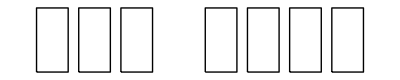

```mathematica
n=3;m=4;
Style[Show[Graphics[{sqs}],AspectRatio->Automatic,PlotRange->{{0,n+m+3/4},{-.01,1.01}},ImageSize->30 (n+m+3/4)],Antialiasing->False]
```

```mathematica
n=4;
Show[Graphics[{sqs,t[1,6],tt[2,7],ttt[3]}],AspectRatio->Automatic,PlotRange->{{0,2 n+3/4},{-3/4,7/4}},ImageSize->30 (2 n+3/4)]
```

```mathematica
n=4;
Show[Graphics[{sqs,t[2,9],ttt[3]}],AspectRatio->Automatic,PlotRange->{{0,2 n+3/4},{-3/4,7/4}},ImageSize->30 (2 n+3/4)]
```

```mathematica
n=4;
Show[Graphics[{sqs,t[2,7],ttt[3]}],AspectRatio->Automatic,PlotRange->{{0,2 n+3/4},{-3/4,7/4}},ImageSize->30 (2 n+3/4)]
```

```mathematica
n=4;
Show[Graphics[{sqs,t[2,7]}],AspectRatio->Automatic,PlotRange->{{0,2 n+3/4},{-3/4,7/4}},ImageSize->30 (2 n+3/4)]
```

```mathematica
n=4;
Show[Graphics[{sqs,t[1,6]}],AspectRatio->Automatic,PlotRange->{{0,2 n+3/4},{-3/4,7/4}},ImageSize->30 (2 n+3/4)]
```

```mathematica
n=4;
Show[Graphics[{sqs,t[4,9]}],AspectRatio->Automatic,PlotRange->{{0,2 n+3/4},{-3/4,7/4}},ImageSize->30 (2 n+3/4)]
```

```mathematica
n=4;
Show[Graphics[{sqs,t[2,6]}],AspectRatio->Automatic,PlotRange->{{0,2 n+3/4},{-3/4,7/4}},ImageSize->30 (2 n+3/4)]
```

```mathematica
n=4;
Show[Graphics[{sqs,ttt[2]}],AspectRatio->Automatic,PlotRange->{{0,2 n+3/4},{-3/4,7/4}},ImageSize->30 (2 n+3/4)]
```

```mathematica
n=4;
Show[Graphics[{sqs,ttt[2],t[4,6]}],AspectRatio->Automatic,PlotRange->{{0,2 n+3/4},{-3/4,7/4}},ImageSize->30 (2 n+3/4)]
```

```mathematica
n=4;
Show[Graphics[{sqs,t[3,6]}],AspectRatio->Automatic,PlotRange->{{0,2 n+3/4},{-3/4,7/4}},ImageSize->30 (2 n+3/4)]
```

```mathematica
n=5;
Show[Graphics[{sqs,tt[2,7],t[5,8],t[3,10]}],AspectRatio->Automatic,PlotRange->{{0,2 n+3/4},{-3/4,7/4}},ImageSize->30 (2 n+3/4)]
```

```mathematica
n=5;
Show[Graphics[{sqs,tt[3,11],t[4,5],t[5,10]}],AspectRatio->Automatic,PlotRange->{{0,2 n+3/4},{-3/4,7/4}},ImageSize->30 (2 n+3/4)]
```

```mathematica
n=5;
Show[Graphics[{sqs,tt[3,11],t[1,8]}],AspectRatio->Automatic,PlotRange->{{0,2 n+3/4},{-3/4,7/4}},ImageSize->30 (2 n+3/4)]
```

```mathematica
n=5;
Show[Graphics[{sqs,tt[3,11],t[4,7]}],AspectRatio->Automatic,PlotRange->{{0,2 n+3/4},{-3/4,7/4}},ImageSize->30 (2 n+3/4)]
```

```mathematica
n=5;
Show[Graphics[{sqs,t[1,5],t[8,9]}],AspectRatio->Automatic,PlotRange->{{0,2 n+3/4},{-3/4,7/4}},ImageSize->30 (2 n+3/4)]
```

```mathematica
n=6;
Show[Graphics[{sqs,t[1,4],tt[2,3],t[9,11],tt[8,13]}],AspectRatio->Automatic,PlotRange->{{0,2 n+3/4},{-3/4,7/4}},ImageSize->30 (2 n+3/4)]
```

```mathematica
n=6;
Show[Graphics[{sqs,ttt[10],t[5,12],tt[6,13],tt[3,6]}],AspectRatio->Automatic,PlotRange->{{0,2 n+3/4},{-3/4,7/4}},ImageSize->30 (2 n+3/4)]
```

```mathematica
n=6;
Show[Graphics[{sqs,t[2,13],t[4,8],tt[5,9],ttt[9]}],AspectRatio->Automatic,PlotRange->{{0,2 n+3/4},{-3/4,7/4}},ImageSize->30 (2 n+3/4)]
```

```mathematica
n=4;
Show[Graphics[{sqs,t[4,9],tt[1,7],tt[8,9],t[3,4]}],AspectRatio->Automatic,PlotRange->{{0,2 n+3/4},{-3/4,7/4}},ImageSize->30 (2 n+3/4)]
```